# Appendix Plots

In this notebook, we present the code used to generate the plots in the paper “Cooling through parametric modulations and phase-preserving quantum measurements.”

Variables used in this notebook 
λ = Squeezing amplitude divided by ω0
ξ = Coherent state parameter of the mechanics
t = Time divided by ω0
ϕ_p = parametric driving phase

Author information
Sofia Qvarfort
Nordita, KTH Royal Institute of Technology and Stockholm University, Hannes Alfvéns väg 12, SE-106 91 Stockholm, Sweden
Department of Physics, Stockholm University, AlbaNova University Center, SE-106 91 Stockholm, Sweden
sofia.qvarfort@fysik.su.se

Error plot for approximate solutions (Fig. 3).

First define the numerical solutions of Mathieu’s equation:

```mathematica
Clear[p11,p11Exact]
PNum[t_] = p[t]/. DSolve[{p''[t]== - (1 + 4 λ Cos[2 t +ϕp]) p[t],p[0]==1, p'[0]==0},p,t][[1]];
QNum[t_] = q[t]/. DSolve[{q''[t]== - (1 + 4  λ Cos[2 t +ϕp]) q[t],q[0]==0, q'[0]==1},q,t][[1]];
```

The approximate solutions (Eq. (11) in the draft) are given by

```mathematica
P[t_] = Exp[- λ t]((Exp[ 2 λ t]- 1)(Sin[t + ϕp] - λ Sin[t]) + λ( Exp[2 λ t ] + 1) Cos[t + ϕp]- (Exp[2 λ t] + 1)Cos[t])/(2 (λ Cos[ϕp]  - 1));
Q[t_] = Exp[- λ t]( (Exp[2 λ t] - 1)Cos[t + ϕp]- (Exp[2λ t] + 1)Sin[t])/(2 (λ Cos[ϕp]- 1));
```

We plot these solutions to demonstrate how accurate they are.

```mathematica
myλ = 0.1;
myϕ =0;
myϕp =π/2;
myr =Sqrt[10];
params = {ϕ-> myϕ,ϕp-> myϕp,r-> myr};
```

```mathematica
PError001= Table[{t,PNum[t]- P[t]/.params /.λ-> 0.01},{t,0,4π,0.1}];
QError001 = Table[{t,QNum[t]- Q[t]/.params /.λ-> 0.01},{t,0,4π,0.1}];
PError005= Table[{t,PNum[t]- P[t]/.params /.λ-> 0.05},{t,0,4π,0.1}];
QError005 = Table[{t,QNum[t]- Q[t]/.params /.λ-> 0.05},{t,0,4π,0.1}];
PError01= Table[{t,PNum[t]- P[t]/.params /.λ->  0.1},{t,0,4π,0.1}];
QError01 = Table[{t,QNum[t]- Q[t]/.params /.λ->  0.1},{t,0,4π,0.1}];
```

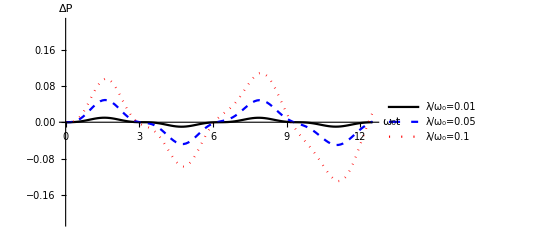

```mathematica
PPlot = ListLinePlot[{ PError001, PError005,PError01}, AxesLabel->{"ω_0t","ΔP"}, Joined-> True, PlotMarkers->None,TicksStyle->Directive[Black,16], AxesLabel->Directive[Black,16], AxesStyle->Directive[Black, 16], PlotRange->{Full,{-0.22,0.22}}, PlotStyle->{Black,{Blue, Dashed},{Red,Dotted}}, PlotLegends->Placed[LineLegend[{"λ/ω_0=0.01","λ/ω_0=0.05","λ/ω_0=0.1"},LegendLayout->{"Column",1}, LegendMarkerSize->20, Spacings-> 0.1],{0.35,0.8}]]
```

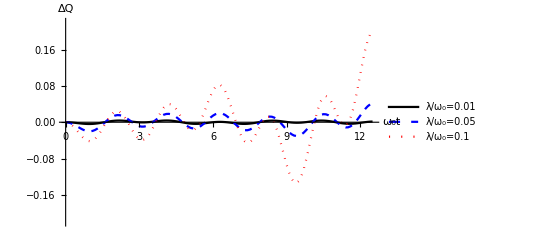

```mathematica
QPlot = ListLinePlot[{ QError001, QError005,QError01}, AxesLabel->{"ω_0t","ΔQ"}, Joined-> True, PlotMarkers->None, PlotLegends->Placed[LineLegend[{"λ/ω_0=0.01","λ/ω_0=0.05","λ/ω_0=0.1"},LegendLayout->{"Column",1}, LegendMarkerSize->20, Spacings-> 0.1],{0.2,0.8}],TicksStyle->Directive[Black,16], AxesLabel->Directive[Black,16], AxesStyle->Directive[Black, 16], PlotRange->{Full, {-0.22, 0.22}}, PlotStyle->{Black,{Blue, Dashed},{Red,Dotted}}]
```

Then define the Bogoliubov coefficients for each solution (Eq. (12) in the draft)

```mathematica
α[t_] =Simplify[(1/2)*(P[t]-  I Q[t] +  D[ I P[tp]+  Q[tp],tp])/.tp-> t];
β[t_] =Simplify[(1/2)* (P[t]+ I Q[t] +  D[I P[tp] - Q[tp],tp] )/.tp-> t];
```

```mathematica
αPer[t_] = ⅇ^(-ⅈ t)-2 ⅈ ⅇ^(-ⅈ t) λ Cos[t+ϕp] Sin[t];
βPer[t_] =-1/4 ⅇ^(-ⅈ (t+ϕp)) (ⅇ^(2 ⅈ ϕp) (-1+ⅇ^(4 ⅈ t))+4 ⅈ t) λ;
```

```mathematica
Simpleα = Normal[Series[α[t],{λ,0,2}] //FullSimplify]
Simpleβ = Normal[ Series[β[t],{λ,0,2}] //FullSimplify]
```

ⅇ^(-ⅈ t)+1/2 λ^2 (ⅇ^(-ⅈ t) t (2 ⅈ+t)-ⅈ ⅇ^(2 ⅈ ϕp) Sin[t])+λ Sin[t] (-ⅈ Cos[ϕp]+Sin[ϕp])

λ (-ⅈ t Cos[t+ϕp]-t Sin[t+ϕp])+1/2 ⅈ λ^2 (Sin[t]+2 t (ⅈ Cos[ϕp]+Sin[ϕp]) Sin[t+ϕp])

```mathematica
αNum[t_] =Simplify[(1/2)*(PNum[t]-  I QNum[t] +  D[ I PNum[tp]+  QNum[tp],tp])/.tp-> t];;
βNum[t_] =Simplify[(1/2)* (PNum[t]+ I QNum[t] +  D[I PNum[tp] - QNum[tp],tp] )/.tp-> t];
```

```mathematica
BogNorm[t_] = Abs[α[t]]^2 - Abs[β[t]]^2;
BogNormNum[t_] = Abs[αNum[t]]^2 - Abs[βNum[t]]^2;
BogNormPer[t_]  = Abs[αPer[t]]^2 - Abs[βPer[t]]^2;
```

```mathematica
myλ = 0.01;
myϕ =0;
myϕp =π/2;
myr =Sqrt[10];
params = {ϕ-> myϕ,λ-> myλ,ϕp-> myϕp,r-> myr};
```

```mathematica
bognormdata = Table[{t,BogNorm[t]/.params },{t,0,4π,0.1}];
bognormdataNum = Table[{t,BogNormNum[t]/.params },{t,0,4π,0.1}];
bognormdataPer = Table[{t,BogNormPer[t]/.params},{t,0,4π,0.1}];
```

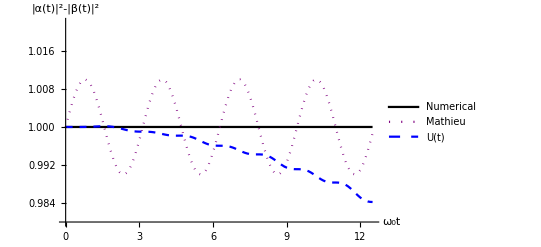

```mathematica
BogNormErrorPlot = ListLinePlot[{ bognormdataNum,bognormdata, bognormdataPer}, AxesLabel->{"ω_0t","|α(t)|^2-|β(t)|^2 "}, Joined-> True, PlotMarkers->None, PlotLegends->Placed[LineLegend[{"Numerical","Mathieu","U(t)"},LegendLayout->{"Row",1}, LegendMarkerSize->20],{0.5,0.9}],PlotStyle->{Black,{Purple, Dotted}, {Blue, Dashed}, {Blue, DotDashed}},TicksStyle->Directive[Black,16], AxesLabel->Directive[Black,16], AxesStyle->Directive[Black, 16], PlotRange->{All,{0.980,1.022}}]
```

Then define the number of quanta for a coherent state (Eq. 16 in the draft).

```mathematica
ada[t_] = Simplify[(Conjugate[α[t]]α[t] + Conjugate[β[t]]β[t])Abs[ξ]^2 + Conjugate[α[t]] β[t]Conjugate[ξ]^2 + α[t]Conjugate[β[t]]ξ^2 + Conjugate[β[t]]β[t] /.ξ-> Exp[I ϕ]r];
```

```mathematica
adaNum[t_] = Simplify[(Conjugate[αNum[t]]αNum[t] + Conjugate[βNum[t]]βNum[t])Abs[ξ]^2 + Conjugate[αNum[t]] βNum[t]Conjugate[ξ]^2 + αNum[t]Conjugate[βNum[t]]ξ^2 + Conjugate[βNum[t]]βNum[t] /.ξ-> Exp[I ϕ]r];
adaPer[t_] = Simplify[(Conjugate[αPer[t]]αPer[t] + Conjugate[βPer[t]]βPer[t])Abs[ξ]^2 + Conjugate[αPer[t]] βPer[t]Conjugate[ξ]^2 + αPer[t]Conjugate[βPer[t]]ξ^2 + Conjugate[βPer[t]]βPer[t] /.ξ-> Exp[I ϕ]r];
ada2S[t_] =Simplify[(Conjugate[α2S[t]]α2S[t] + Conjugate[β2S[t]]β2S[t])Abs[ξ]^2 + Conjugate[α2S[t]] β2S[t]Conjugate[ξ]^2 + α2S[t]Conjugate[β2S[t]]ξ^2 + Conjugate[β2S[t]]β2S[t] /.ξ-> Exp[I ϕ]r];
```

Generate the data and plot the result (Fig. 3 in the draft).

```mathematica
myλ = 0.01;
myϕ =0;
myϕp =π/2;
myr =Sqrt[10];
params = {ϕ-> myϕ,λ-> myλ,ϕp-> myϕp,r-> myr};
```

```mathematica
data = Table[{t,ada[t]/.params },{t,0,4π,0.1}];
dataNum = Table[{t,adaNum[t]/.params },{t,0,4π,0.1}];
dataPer = Table[{t,adaPer[t]/.params},{t,0,4π,0.1}];
data2S = Table[{t,ada2S[t]/.params},{t,0,2π,0.05}];
```

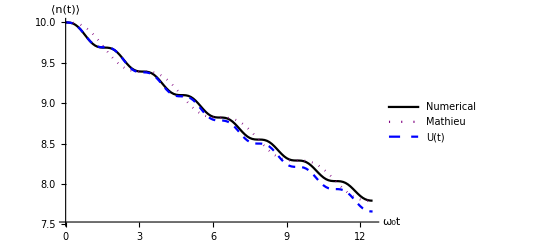

```mathematica
ErrorPlot = ListLinePlot[{ dataNum,data, dataPer}, AxesLabel->{"ω_0t","⟨n(t)⟩"}, Joined-> True, PlotMarkers->None, PlotLegends->Placed[LineLegend[{"Numerical","Mathieu","U(t)"},LegendLayout->{"Column",1}, LegendMarkerSize->20],{0.8,0.8}],  PlotStyle->{Black,{Purple, Dotted}, {Blue, Dashed}, {Blue, DotDashed}},TicksStyle->Directive[Black,16], AxesLabel->Directive[Black,16], AxesStyle->Directive[Black, 16]]
```

Mathieu equation stability plot (Fig. 4).

Generate data for the MathieuC functions, which are built-in numerical functions for Mathematica. Let them tun to a long time, t = 1000. Then create a binary map of regions where the solution diverges (becomes larger than 1000).

```mathematica
table=ParallelTable[{a,q,If[Abs[Re[MathieuC[a,q,1000]]]≥100,1,0]},{a,0,15,0.05},{q,-15,15,0.05}];
```

Define the line that goes at a = 1.

```mathematica
lineStyle={Thick,Red,Dashed};
line=Line[{{1,-15},{1,15}}];
```

Plot the results.

```mathematica
mathieustability = ListDensityPlot[Flatten[table,1], FrameLabel->{"a","ϵ"},   TicksStyle->Directive[Black,16],FrameStyle->Directive[Black,16], AxesStyle->Directive[Black, 16], ColorFunction->(If[#<0.5,White,RGBColor[0.5,0.2,0.43]]&), Epilog->{Directive[Black, Dashed],line}]
```

-Graphics-

Homodyne measurement phase plot (Fig. 5).

First we define the expectation values.

```mathematica
ada = Exp[- x^2]Sum[n /(π^(1/2) 2^n n!) HermiteH[n,x]^2,{n,0,20}];
ad2 = Exp[- x^2]Sum[1/(π^(1/2) 2^(n+1)(n!)) HermiteH[n,x]HermiteH[n+2,x]Exp[-2 I θ],{n,0,20}];
a2 = Conjugate[ad2];;
```

Then we define the number of quanta, using the Bogoliubov coefficients for the approximate solutions_

```mathematica
adaHom[t_] =Conjugate[αNum[t]]βNum[t] ad2 + Conjugate[βNum[t]]αNum[t]a2 + Abs[αNum[t]]^2 ada + Abs[βNum[t]]^2 (ada + 1);
```

Then define the parameters needed and plot the solutions.

```mathematica
myλ= 0.02;
myθ = 0;
myx =0.5;
paramsHom = {λ-> myλ, θ-> myθ, x-> myx};
```

Plot the result for different phase choices.

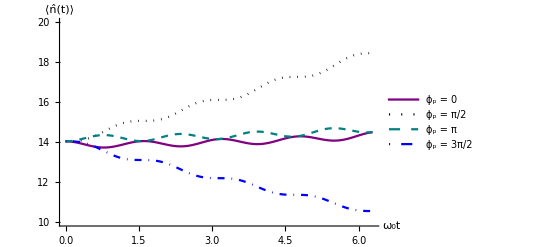

```mathematica
HomodynePlot = Plot[{adaHom[t]/.paramsHom/.ϕp-> 0, adaHom[t]/.paramsHom/.ϕp-> π/2, adaHom[t]/.paramsHom/.ϕp-> π, adaHom[t]/.paramsHom/.ϕp-> 3π/2}, {t,0,2π},AxesLabel->{"ω_0t","⟨n̂(t)⟩"}, PlotLegends->Placed[LineLegend[{"ϕ_p = 0","ϕ_p = π/2", "ϕ_p = π", "ϕ_p = 3π/2"} ,  LegendLayout->{"Row",2}], {0.45, 0.9}],  PlotStyle->{Purple,{Black, Dotted},{RGBColor[0,0.5,0.5],Dashed},{Blue, DotDashed}},TicksStyle->Directive[Black,16], AxesLabel->Directive[Black,16], AxesStyle->Directive[Black, 16], PlotRange->{All, {10,20}}]
```